```mathematica
Needs["QuantumInformation`"];
Needs["MaTeX`"];
```

```mathematica
fixPlots = {Plot, ListPlot, ListLogLogPlot, LogLogPlot};
Table[  SetOptions[ plt
		, Frame -> True
		, FrameTicksStyle-> Directive[ "Helvetica", Black,  13] 
		, LabelStyle ->  Directive[ "Helvetica", Black,  11] 
	];
	,{plt, fixPlots}];
```

## v1: Testing stuff, brute force calculations

## Driving the middle of the star graph

```mathematica
czint[ q1_, q2_, nq_ ]:= (1/4) * (  qop[Z, q1, nq].qop[Z,q2,nq] - qop[Z,q1, nq] - qop[Z,q2,nq] + IdentityMatrix[4] );
parityint[ q1_, q2_, nq_ ] := (1/2) * ( qop[ SparseArray[ Z ], q1, nq ] . qop[ SparseArray[ Z ], q2, nq ] + IdentityMatrix[ 2^nq, SparseArray ] )
```

```mathematica
nq = 5;
graph = AdjacencyMatrix@StarGraph[nq];
ham = graphToHam[ graph, { {Z/2,Z/2} }] ;
basis = allstatestr[ 2, nq ] ;
sss = particlesubspaces[nq];
ss1 = sss[[2]];

swap1 = swapMatrix[ 2^nq, 0 , 2^(nq-1), -Pi/2, -Pi/2 ] ;
swap2 = swapMatrix[ 2^nq,2^nq -1,2^nq-1 -2^(nq-1), -Pi/2, -Pi/2 ];
swapgoal = swap1.swap2;
```

```mathematica
w = 4;
Ts = Range[ 2 Pi, 10Pi, 2 Pi ];
res = Table[
A = Pi / Tval;
hamall = ham + A Cos[w t] qop[X,1,nq];
sol = evolveUnitary2[ hamall, {t,0,Tval} ];
{Tval, TraceError[ swapgoal, sol /. t-> Tval  ]}
,{Tval,Ts} ]
```

{{2 π,0.00423838},{4 π,0.0010796},{6 π,0.000481587},{8 π,0.000271309},{10 π,0.000173813}}

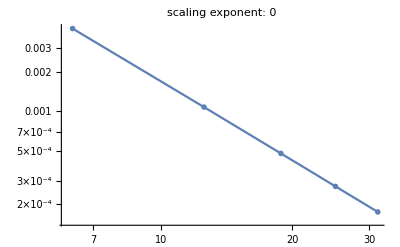

```mathematica
expfit = exponentFit[ res ] ;
ListLogLogPlot[ res,  PlotLabel-> "scaling exponent: " <> ToString@expfit[[2]] ]
```

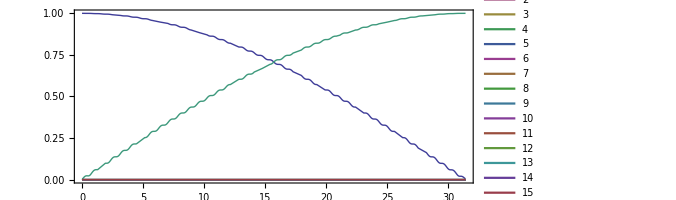

```mathematica
Plot[ Evaluate@Abs@sol[[1]], {t,0,Ts[[-1]]} ]
```

#### Scaling with N:

```mathematica
nqs = Range[2,7];
Ts = Range[4,10,2]* 2 Pi;
errvsNq = Table[

A = Pi / T;
graph = AdjacencyMatrix@StarGraph[nq];
ham = graphToHam[ graph, { {Z/2,Z/2} }] ;

swap1 = swapMatrix[ 2^nq, 0 , 2^(nq-1), -Pi/2, -Pi/2 ] ;
swap2 = swapMatrix[ 2^nq,2^nq -1,2^nq-1 -2^(nq-1), -Pi/2, -Pi/2 ];
swapgoal = swap1.swap2;

w = Max[ Diagonal[ham] ] - Min[ Diagonal[ham]];

hamall = ham + A Cos[w t] qop[X,1,nq];
sol = evolveUnitary2[ hamall, {t,0,T} ];
{nq, T,  TraceError[ swapgoal, sol /. t-> T  ]}
,{nq, nqs}, {T,Ts} ]
```

$Aborted

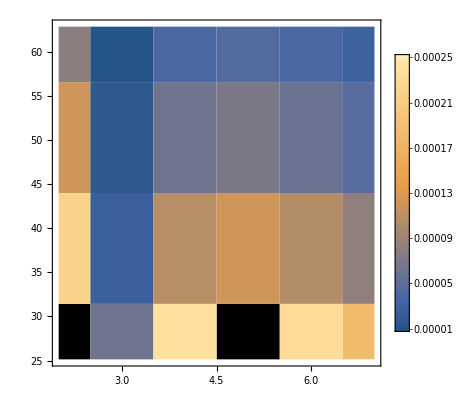

```mathematica
flaterrnq = Flatten[errvsNq,1 ] ;
ListContourPlot[ flaterrnq, InterpolationOrder->0, Contours -> 100, PlotLegends->Automatic, ClippingStyle->{White,Black}]
```

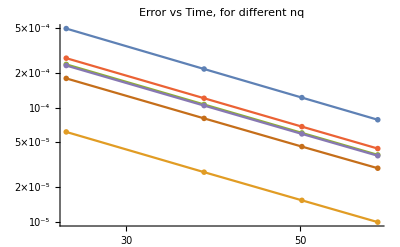

```mathematica
cols = ColorData[97, "ColorList"];
legnq = LineLegend[  cols, nqs ];
legts = LineLegend[  cols, Ts ];
{ Show[ Table[
ListLogLogPlot[ errvsNq[[j]][[All,{2,3} ]], PlotStyle->cols[[j]] ]
,{j,1,Length[nqs]}]
, PlotRange-> All, PlotLabel-> "Error vs Time, for different nq"  ], legnq }
```

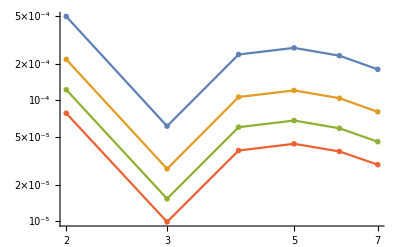

```mathematica
{ Show[ Table[
ListLogLogPlot[ errvsNq[[All,j, {1,3}]], PlotStyle->cols[[j]] ]
,{j,1,Length[Ts]}]
, PlotRange-> All ], legts }
```

## Generating symmetric states... woops, we don’t even need to!

```mathematica
nq = 5;
graph = AdjacencyMatrix@StarGraph[nq];
ham = graphToHam[ graph, { {Z/2,Z/2} }] ;
basis = allstatestr[ 2, nq ] ;
sss = particlesubspaces[nq];
ss1 = sss[[2]];
```

```mathematica
(* Generate all symmetric states *)
generator = Sum[ qop[splus, j, nq] , {j,2,nq}];
rootstates = { Vec[0,2^nq], qop[X,1,nq] . Vec[0,2^nq] };
order = 4;
symmstates = { rootstates };
Do[ AppendTo[ symmstates, Table[ generator.s ,{s,symmstates[[-1]]} ] ] , { j, 1, order } ]
symflat = Normalize /@ Flatten[symmstates, 1 ] ;
```

```mathematica
hdrive = qop[X,1,nq];
```

## Looking at TLSs

```mathematica
nq = 5;
graph = AdjacencyMatrix@StarGraph[nq];
ham = graphToHam[ graph, { {Z/2,Z/2} }] ;
basis = allstatestr[ 2, nq ] ;
sss = particlesubspaces[nq];
ss1 = sss[[2]];

T = 10Pi;
A = Pi / T;
w = Max[#] - Min[#] &@ Diagonal[ham];
hamall = ham + A Cos[w t] qop[X,1,nq];
```

```mathematica
(* The transitioning states *)
v1 = Vec[0,2^nq];
v2 = qop[X,1,nq].v1;
idxs = Flatten@{Position[v1,1], Position[v2,1] } ;
sol = evolveUnitary2[ hamall[[idxs,idxs ]], {t,0,T} ] /. t-> T;
err1 = TraceError[ I X, sol  ]
tr1 = Tr[I X . sol ]

v1 = Vec[2^nq-1,2^nq];
v2 = qop[X,1,nq].v1;
idxs = Flatten@{Position[v1,1], Position[v2,1] } ;
sol = evolveUnitary2[ hamall[[idxs,idxs ]], {t,0,T} ] /. t-> T;
err2 = TraceError[ I X, sol  ]
tr2 = Tr[I X . sol ]
```

```mathematica
(* States that do not transition *)
noflipres = Table[
v1 = Vec[j,2^nq];
v2 = qop[X,1,nq].v1;
idxs = Flatten@{Position[v1,1], Position[v2,1] } ;
sol = evolveUnitary2[ hamall[[idxs,idxs ]], {t,0,T} ] /. t-> T;
 err= TraceError[ Id2, sol ];
tr = Tr[sol];
{err,tr}
,{j,1,2^(nq-1)-2} ];
nofliperrors = noflipres[[All,1]];
nofliptraces = noflipres[[All,2]];
```

```mathematica
1 - (1/2^nq) * Total@Join[{tr1,tr2}, nofliptraces ]
Mean[nofliperrors]
```

0.000173494+0. ⅈ

0.000195492

```mathematica
swap1 = swapMatrix[ 2^nq, 0 , 2^(nq-1), -Pi/2, -Pi/2 ] ;
swap2 = swapMatrix[ 2^nq,2^nq -1,2^nq-1 -2^(nq-1), -Pi/2, -Pi/2 ];
swapgoal = swap1.swap2;
```

```mathematica
(* Compare to normal evolution (full ham) *)
sol = evolveUnitary2[ hamall, {t,0,T} ] /. t-> T;
TraceError[ swapgoal, sol ]
```

0.000173813

## Simulation of independent TLS’s

Note: We can correct for Non-HWP cases simply by multiplying by Exp[ + t DiagonalMatrix[ { n-w, w } ]

```mathematica
StarTLSHam[n_, w_ ]:= DiagonalMatrix[{n/2-w, w-n/2}];  (* note that we subtracted (n/2) * Identity, to avoid overall phases *)
multiplicity[ n_, w_ ]:= Binomial[ n ,w ];
multiplicities[ n_ ] := Table[ multiplicity[ n, w ], {w,0,n} ];

(* If SinY is not included, then w=0 and w=n are a flip matrix. If SinY is included, then only w=0 is a flip matrix *)
goalmatrix[n_, w_, fi1_:0, includeSinY_:False ] := Module[{},
	If[ w==0,  Return[ -I ( Cos[fi1] X + Sin[fi1] Y ) ] ];
	If[ w==n && Not[ includeSinY ], Return[ -I ( Cos[-fi1] X + Sin[-fi1] Y ) ] ];
	Return[ Id2 ];
];


(* Simulate all TLSes of the specified system, return the final states *)
StarDriveHWP[ n_, T_, fi1_:0, includeSinY_:False, includeHWP_:True ] := Module[{omega, A,fi2, drive, simress, s1, s2, t},
	omega = n;
	A = Pi / T;
	fi2 = -fi1 - omega T / 2 ;
	
	drive[f_] := If[ includeSinY
		, A * (1/2) * ( Cos[ omega t  + f ] X + Sin[ omega t + f ] Y )
		, A Cos[ omega t  + f ] X 
	];
	
	If[ includeHWP,
		simress = Table[ 
			s1 = evolveUnitary[ StarTLSHam[n,w] + drive[fi1] , {t,0,T/2} ];
			s2 = evolveUnitary[ StarTLSHam[n,w] + drive[fi2] , {t,0,T/2} ];
			X.s2[T/2].X.s1[T/2]
			,{w,0,n}];
		, simress = Table[ evolveUnitary[ StarTLSHam[n,w] + drive[fi1] , {t,0,T} ][T] ,{w,0,n}];
	];
	Return[simress];
];

(* Given final states, find the trace error

 To prevent traces larger than dim(H) in highly optimal cases, we have a few options:
 1) divide by the norm of simress[[w]]
 2) orthogonalize simress[[w]]
 For now, we choose to do the latter.
   *)
simressToTraces[ simress_ , fi1_:0, includeSinY_:False ]:= Module[{n},
	n = Length[simress]-1;
	Return[  Table[ 
		Tr[ ( Normalize /@ simress[[w+1]]  ). ConjugateTranspose[ goalmatrix[ n , w, fi1, includeSinY ] ] ]
	, {w, 0, n}] ];
];

simressToOpNorms[ simress_, fi1_:0, includeSinY_:False ]:= Module[{n},
	n = Length[simress]-1;
	Return[  Table[ 
		Norm[ ( Normalize /@ simress[[w+1]] ) - goalmatrix[ n, w, fi1, includeSinY ] ]
	, {w, 0, n}] ];
];



(* Find the trace error of a given gate. Be warned: If includeHWP is off, then only on T~k*2Pi low error can be expected  *)
StarDriveErrorHWP[ n_, T_, fi1_:0, includeSinY_:False, includeHWP_:True ] := Module[{simress, traces},
	simress = StarDriveHWP[ n, T, fi1, includeSinY, includeHWP ];
	traces = simressToTraces[simress, fi1, includeSinY ];
	Return[ 1 - Abs[(traces.multiplicities[n])] / (2^(n+1)) ];
];


(* Largest eigenvalue (in Result - Expected), the operator norm *)
StarDriveNormHWP[ n_, T_, fi1_:0, includeSinY_:False, includeHWP_:True ] := Module[{simress, norms},
	simress = StarDriveHWP[ n, T, fi1, includeSinY, includeHWP ];
	norms = simressToOpNorms[simress, fi1, includeSinY ];
	Return[ Max[ norms ] ];
];


(* The phases of this model are trivial - why not invert all obtained phases (in the case of no HWP) *)
phaseRestore[ n_, w_, T_ ]:= MatrixExp[ + I T StarTLSHam[n,w] ];

StarDriveErrorPhaseCorrected[ n_, T_, fi1_:0, includeSinY_:False ] := Module[{simress, traces},
	simress = StarDriveHWP[ n, T, fi1, includeSinY, False ];
	 (* apply another gate, which performs reverse time evolution *)
	simress = Table[ phaseRestore[ n, w, T ] . simress[[w+1]], {w, 0, n} ];
	traces = simressToTraces[simress, fi1, includeSinY ];
	Return[ 1 - Abs[(traces.multiplicities[n])] / (2^(n+1)) ];
];

StarDriveNormPhaseCorrected[ n_, T_, fi1_:0, includeSinY_:False ] := Module[{simress, norms},
	simress = StarDriveHWP[ n, T, fi1, includeSinY, False ];
	 (* apply another gate, which performs reverse time evolution *)
	simress = Table[ phaseRestore[ n, w, T ] . simress[[w+1]], {w, 0, n} ];
	norms = simressToOpNorms[simress, fi1, includeSinY ];
	Return[ Max[ norms ] ];
];


showSimRess[ simress_ ]:= MatrixForm[ MatrixForm /@ Round[ simress, 0.01 ] ];
```

#### small tests

Varying f1

```mathematica
n=3;
Ts = Range[20,40,.2];  
T = 20Pi;
fi1s = Range[0,Pi, .1 ];
includeSinY = False;
includeHWP = False;

params = fi1s; 
errs=  Table[ {param, StarDriveErrorHWP[ n, T, param, includeSinY, includeHWP ] }, {param,params} ];
```

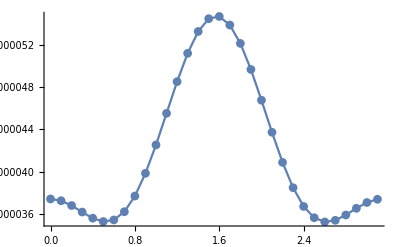

```mathematica
ListPlot[ errs ]
```

Varying T

```mathematica
n=3;
Ts = Range[2,10] * Pi;
fi1 = 1;
includeSinY = False;
includeHWP = False;

params = Ts; 
errs=  Table[ {param, StarDriveErrorHWP[ n, param, fi1, includeSinY, includeHWP ] }, {param,params} ];
```

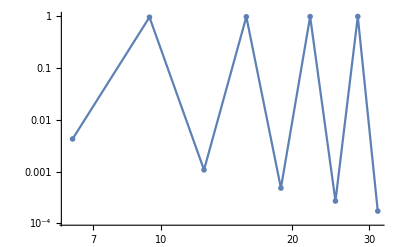

```mathematica
ListLogLogPlot[errs]
```

#### Large scale behaviour of our gate:

Decay over time

```mathematica
ns = {1,2,3};
Ts = Range[2,20,.2];
ers = Table[ StarDriveErrorHWP[ n, T, 0 ], {n,ns}, {T,Ts} ];
ersWSin = Table[ StarDriveErrorHWP[ n, T, 0, True ], {n,ns}, {T,Ts} ];
```

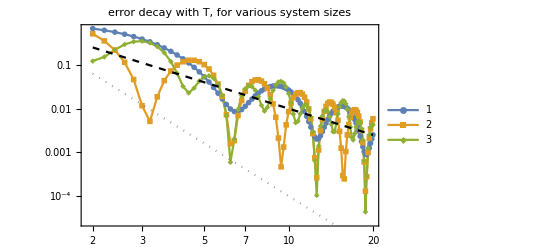

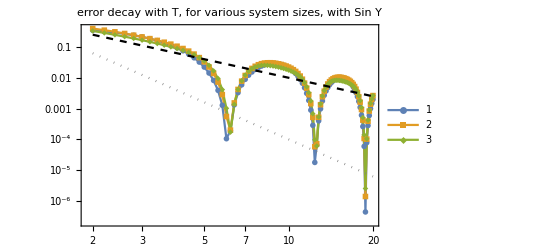

```mathematica
(* Decay over time... for various n *)
Show[{
ListLogLogPlot[ 
Table[ {Ts, ers[[nidx]]}ᵀ, {nidx, 1, Length[ns]}]
 , PlotLegends->ns
, PlotLabel -> "error decay with T, for various system sizes"
, GridLines->{ Range[2Pi, 10Pi, 2 Pi], {}}
]
, LogLogPlot[ {x^(-2), x^(-4) }, {x,Min[Ts], Max[Ts] }, PlotStyle->{ Directive[Black, Dashed], Directive[ Gray, Dotted] } ]
}]

(* Decay over time... including SIN driving field. *)
Show[{
ListLogLogPlot[ 
Table[ {Ts, ersWSin[[nidx]]}ᵀ, {nidx, 1, Length[ns]}]
 , PlotLegends->ns
, PlotLabel -> "Err vs T, for various system sizes, with Sin Y"
, GridLines->{ Range[2Pi, 10Pi, 2 Pi], {}}
]
, LogLogPlot[ {x^(-2), x^(-4) }, {x,Min[Ts], Max[Ts] }, PlotStyle->{ Directive[Black, Dashed], Directive[ Gray, Dotted] } ]
}]
```

Error scaling as function of n.

```mathematica
(* Error scaling as function of n *)
ns = Round[2^Range[1,7,.5]];
T = 6 Pi;
ersVsN = Table[ StarDriveErrorHWP[ n, T ], {n,ns} ];
ersWSinVsN= Table[ StarDriveErrorHWP[ n, T , 0 , True ], {n,ns} ];
```

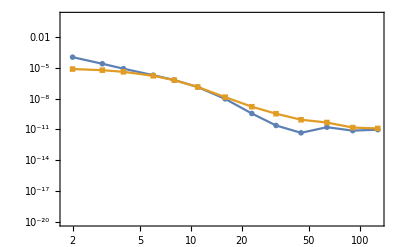

```mathematica
(* The scaling here is highly dependent on the we we enforce non-negative results: normalizing the output vectors *)
ListLogLogPlot[ { {ns, ersVsN}ᵀ, {ns, ersWSinVsN}ᵀ } , PlotRange->{10^-20, 1} ]
```

#### Can we predict the “kink” in the error (presumably a numerical error?)

```mathematica
ns = Round[2^Range[1,7,.5]];
Ts = Range[ 2Pi, 8 Pi, 2 Pi ];
ers = Table[ {n, T, StarDriveErrorHWP[ n, T ]}, {n,ns}, {T,Ts} ];
```

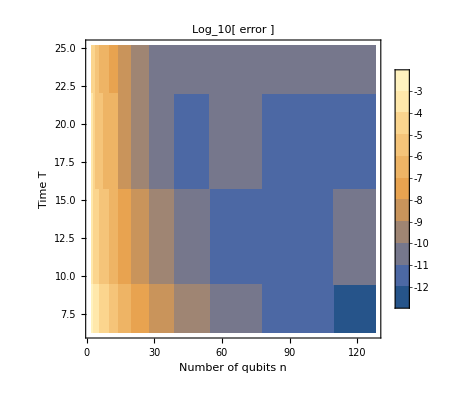

```mathematica
ersflat = Flatten[ers, 1 ];
erslog = ersflat * 1;
erslog[[All,-1]] = Log[ erslog[[ All, -1 ]] ] / Log[10];
ListContourPlot[ erslog, InterpolationOrder->0, PlotLegends->Automatic
, PlotLabel->"Log_10[ error ]"
, FrameLabel->{ "Number of qubits n", "Time T" } ]
```

Actual decay with time, for various n

```mathematica
cols = Table[ Hue[ .7,1 ,(n/Max[ns])^.4  ], {n, ns } ]
tdecayplt = ListLogLogPlot[ ers[[All, All, {2,3}]]
, PlotStyle->cols
, PlotLegends->ns
, PlotLabel->"Error decay with time, for various n"
, FrameTicks-> {{Automatic, Automatic},{Ts, Automatic} }

, FrameLabel->{MaTeX["T/J", Magnification->1.3], MaTeX["\\mathcal{E}", Magnification->1.3]}
]
```

{Hue[0.7, 1, 0.18946457081379975],Hue[0.7, 1, 0.2228253072457504],Hue[0.7, 1, 0.24999999999999997],Hue[0.7, 1, 0.2940197556311684],Hue[0.7, 1, 0.32987697769322355],Hue[0.7, 1, 0.3746908487139812],Hue[0.7, 1, 0.43527528164806206],Hue[0.7, 1, 0.5032770731958376],Hue[0.7, 1, 0.5743491774985174],Hue[0.7, 1, 0.6582653841049738],Hue[0.7, 1, 0.757858283255199],Hue[0.7, 1, 0.8724339733949449],Hue[0.7, 1, 1.]}

Part::partd: Part specification «1» is longer than depth of object.

ListLogLogPlot::lpn: «1» is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogLogPlot::lpn will be suppressed during this calculation.

ListLogLogPlot[{{0.675274,0.617983,0.559647,0.501355,0.444161,0.389042,0.336848,0.288269,0.243811,0.203783,0.168304,0.137325,0.110657,0.0880121,0.0690369,0.053355,0.0405939,0.0304071,0.0224857,0.0165611,0.0124009,0.00980001,0.00857001,0.00852906,0.00949386,0.011275,0.0136762,0.0164963,0.0195347,0.0225978,0.0255065,0.0281032,0.0302575,0.031871,0.0328792,0.0332518,0.0329918,0.0321315,0.0307285,0.0288601,0.0266177,0.0241007,0.0214113,0.0186493,0.0159084,0.013273,0.0108159,0.00859716,0.0066636,0.00504867,0.00377297,0.00284496,0.00226177,0.00201014,0.00206734,0.00240229,0.00297664,0.00374613,0.004662,0.00567266,0.0067255,0.00776877,0.00875349,0.0096353,0.0103761,0.0109453,0.0113211,0.0114908,0.011451,0.0112073,0.0107736,0.010171,0.00942669,0.00857194,0.007641,0.00666929,0.00569194,0.00474241,0.00385135,0.00304562,0.00234757,0.0017745,0.0013384,0.00104578,0.000897762,0.000890265,0.00101437,0.00125677,0.0016004,0.0020251,0.00250844},{0.513155,0.353155,0.217556,0.114197,0.046146,0.0116503,0.00510585,0.0186204,0.0436593,0.0723845,0.0985085,0.117674,0.127478,0.127284,0.117925,0.101351,0.0802508,0.0576385,0.0364354,0.0190808,0.00722799,0.00157397,0.00185172,0.00697598,0.0153024,0.0249406,0.0340597,0.0411413,0.0451508,0.0456209,0.0426514,0.0368378,0.0291429,0.0207314,0.012787,0.00633854,0.00211676,0.000466021,0.00132059,0.00424676,0.00853896,0.0133493,0.0178266,0.0212429,0.0230895,0.0231332,0.0214291,0.0182919,0.0142324,0.00987006,0.00583432,0.00266933,0.000756047,0.000263325,0.00113442,0.0031094,0.00577766,0.00865029,0.0112392,0.0131308,0.0140432,0.0138601,0.012639,0.0105925,0.00804843,0.00539499,0.00301872,0.00124575,0.000294469,0.00024704,0.00104323,0.00249674,0.00433032,0.00622295,0.00786128,0.00898687,0.00943275,0.00914418,0.00818168,0.00670673,0.00495286,0.00318708,0.00166765,0.000604649,0.000129525,0.000277845,0.000987718,0.00211343,0.00345154,0.00477469,0.00586763},{0.12184,0.151882,0.221858,0.293157,0.339409,0.348337,0.31963,0.261936,0.189677,0.119179,0.0642054,0.0321934,0.0228246,0.0294776,0.0426076,0.053363,0.0561241,0.0494869,0.03584,0.0199342,0.00694142,0.000593149,0.00200126,0.00953299,0.0196852,0.0285089,0.0329992,0.0319943,0.0263814,0.0186343,0.0118745,0.0087686,0.0106276,0.0170122,0.0259597,0.0347083,0.0406226,0.0419981,0.0385094,0.0312111,0.0221291,0.013586,0.00747957,0.0047436,0.00516197,0.00757592,0.0103795,0.0121068,0.0119053,0.00975568,0.00639175,0.00297403,0.000641909,0.000103658,0.00140543,0.00395136,0.00675233,0.0087995,0.00942327,0.00851508,0.006545,0.00437866,0.00296195,0.00298375,0.00463371,0.00753689,0.0108829,0.0136977,0.0151594,0.0148527,0.0128831,0.00982232,0.00650918,0.00377669,0.00219524,0.00191636,0.00266398,0.0038673,0.00488087,0.0052113,0.0046739,0.00343221,0.00191465,0.000644086,0.0000433905,0.000286019,0.00124278,0.00253969,0.00370155,0.00432667,0.00422977}}⟦All,All,{2,3}⟧,PlotStyle→{Hue[0.7, 1, 0.18946457081379975],Hue[0.7, 1, 0.2228253072457504],Hue[0.7, 1, 0.24999999999999997],Hue[0.7, 1, 0.2940197556311684],Hue[0.7, 1, 0.32987697769322355],Hue[0.7, 1, 0.3746908487139812],Hue[0.7, 1, 0.43527528164806206],Hue[0.7, 1, 0.5032770731958376],Hue[0.7, 1, 0.5743491774985174],Hue[0.7, 1, 0.6582653841049738],Hue[0.7, 1, 0.757858283255199],Hue[0.7, 1, 0.8724339733949449],Hue[0.7, 1, 1.]},PlotLegends→{2,3,4,6,8,11,16,23,32,45,64,91,128},PlotLabel→Error decay with time, for various n,FrameTicks→{{Automatic,Automatic},{{2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.},Automatic}},FrameLabel→{-Graphics-,-Graphics-}]

```mathematica
Export["starTdecayVariousN.pdf", tdecayplt ]
```

starTdecayVariousN.pdf

#### Decay over time, without HWP

Moral of the story: TraceAVG DECREASES with N (as espected). The OperatorNorm is pretty much CONSTANT (or converges to a reasonable value quickly).

```mathematica
ns = {2, 3, 6, 10};
Ts = Range[2,20,.2];
```

```mathematica
(* Trace Errors most vanilla: without HWP, but phase corrected. *)
ers = Table[ StarDriveErrorPhaseCorrected[ n, T, 0, False  ], {n,ns}, {T,Ts} ];
ersSin = Table[ StarDriveErrorPhaseCorrected[ n, T, 0, True  ], {n,ns}, {T,Ts} ];
```

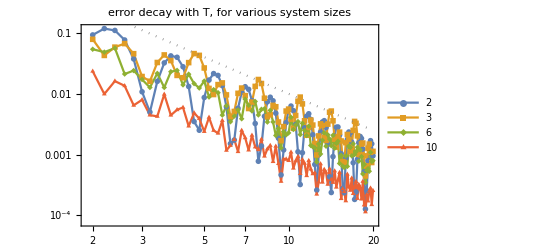

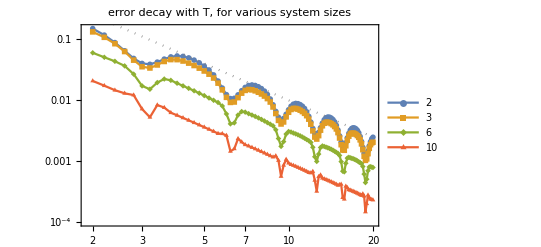

```mathematica
(* Decay over time... for various n *)
Show[{
ListLogLogPlot[ 
Table[ {Ts, ers[[nidx]]}ᵀ, {nidx, 1, Length[ns]}]
 , PlotLegends->ns
, PlotLabel -> "error decay with T, for various system sizes"
, GridLines->{ Range[2Pi, 10Pi, 2 Pi], {}}
]
, LogLogPlot[ {x^(-2) }, {x,Min[Ts], Max[Ts] }, PlotStyle->{ Directive[Black, Dashed], Directive[ Gray, Dotted] } ]
}]

(* Decay over time... for various n *)
Show[{
ListLogLogPlot[ 
Table[ {Ts, ersSin[[nidx]]}ᵀ, {nidx, 1, Length[ns]}]
 , PlotLegends->ns
, PlotLabel -> "error decay with T, for various system sizes"
, GridLines->{ Range[2Pi, 10Pi, 2 Pi], {}}
]
, LogLogPlot[ {x^(-2) }, {x,Min[Ts], Max[Ts] }, PlotStyle->{ Directive[Black, Dashed], Directive[ Gray, Dotted] } ]
}]
```

```mathematica
ers2 = Table[ StarDriveNormPhaseCorrected[n, T, 0, False ], {n,ns}, {T,Ts} ];
```

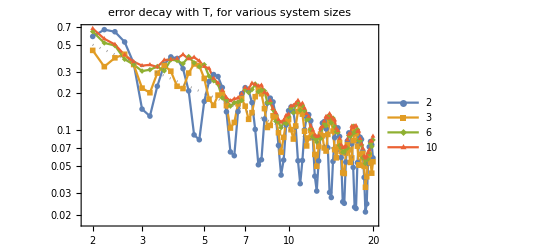

```mathematica
(* Decay over time... for various n *)
Show[{
ListLogLogPlot[ 
Table[ {Ts, ers2[[nidx]]}ᵀ, {nidx, 1, Length[ns]}]
 , PlotLegends->ns
, PlotLabel -> "error decay with T, for various system sizes"
, GridLines->{ Range[2Pi, 10Pi, 2 Pi], {}}
]
, LogLogPlot[ {x^(-1) }, {x,Min[Ts], Max[Ts] }, PlotStyle->{ Directive[Black, Dashed], Directive[ Gray, Dotted] } ]
}]
```

```mathematica
ers3 = Table[ StarDriveNormHWP[n, T, 0, False ], {n,ns}, {T,Ts} ];
```

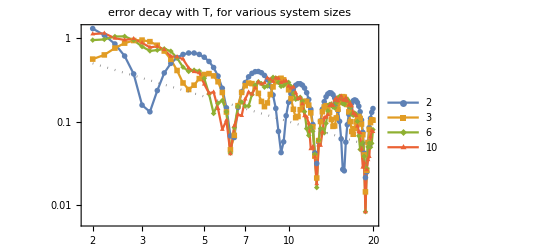

```mathematica
(* Decay over time... for various n *)
Show[{
ListLogLogPlot[ 
Table[ {Ts, ers3[[nidx]]}ᵀ, {nidx, 1, Length[ns]}]
 , PlotLegends->ns
, PlotLabel -> "error decay with T, for various system sizes"
, GridLines->{ Range[2Pi, 10Pi, 2 Pi], {}}
]
, LogLogPlot[ {x^(-1) }, {x,Min[Ts], Max[Ts] }, PlotStyle->{ Directive[Black, Dashed], Directive[ Gray, Dotted] } ]
}]
```

## v2: Analytics

#### Sanity check: full matrix calculations, for Trace errors.

```mathematica
traceErrorOldSlow[ n_, T_ ] := Module[{ham, repl, Uw, UrotConj, FidTr, traces, tracetotal, w, A},
	ham = w Z + A X;
	repl = A -> Pi/ 2 / T;
	Uw = FullSimplify @ MatrixExp[-I ham T /. repl] ;
	UrotConj = MatrixExp[ + I w Z T ] ;
	FidTr = FullSimplify[  Tr[ Uw . UrotConj ]  ];
	traces = Join[ {2}, Table[ FidTr,{w,1,n} ]  ];
	tracetotal = Simplify[ multiplicities[n] . traces / 2^(n+1)  ];

	Return[1-tracetotal];
];

traceError[ n_, T_ ] := Module[{vvec, vhat,  Uw, UrotConj, FidTr, traces, tracetotal, w, A},
	
	traces = Join[{2},
		Table[ 
			vvec = { Pi/2/T, 0, w };
			vhat = Normalize[ vvec]; 
			Uw = Cos[ Norm[vvec] T ] * Id2 -I Sin[ Norm[vvec] T ] * (vhat[[1]] X + vhat[[3]] Z);
			UrotConj = Cos[ w T ]*Id2 +I Sin[ w  T ] * Z;
			FidTr = Simplify[  Tr[ Uw . UrotConj ]  ]
			, {w,1,n}] 
	];
	tracetotal = Simplify[ multiplicities[n] . traces / 2^(n+1), T>0 ];

	Return[1-tracetotal];
];
```

```mathematica
Clear[n, T, A, w]
n= 4;
repl = A -> Pi/ 2 / T;

(* Analytical derivation *)
ham = w Z + A X;
Uw = FullSimplify @ MatrixExp[-I ham T /. repl] 
UrotConj = MatrixExp[ + I w Z T ] ;
FidTr = FullSimplify[  Tr[ Uw . UrotConj ]  ]
traces = Join[ {2}, Table[ FidTr,{w,1,n} ]  ];
tracetotal = Simplify[ multiplicities[n] . traces / 2^(n+1)  ];

traceError[n, T] == 1-tracetotal
```

{{Cos[1/2 √(π^2+4 T^2 w^2)]-(2 ⅈ T w Sin[1/2 √(π^2+4 T^2 w^2)])/(√(π^2+4 T^2 w^2)),-(ⅈ π Sin[1/2 √(π^2+4 T^2 w^2)])/(√(π^2+4 T^2 w^2))},{-(ⅈ π Sin[1/2 √(π^2+4 T^2 w^2)])/(√(π^2+4 T^2 w^2)),Cos[1/2 √(π^2+4 T^2 w^2)]+(2 ⅈ T w Sin[1/2 √(π^2+4 T^2 w^2)])/(√(π^2+4 T^2 w^2))}}

2 Cos[T w] Cos[1/2 √(π^2+4 T^2 w^2)]+(4 T w Sin[T w] Sin[1/2 √(π^2+4 T^2 w^2)])/(√(π^2+4 T^2 w^2))

True

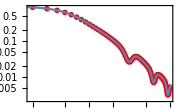

```mathematica
(* For comparison with numerical results *)
Ts = Range[.2, 10, .1];
ersSin = Table[ {T, StarDriveErrorPhaseCorrected[ n, T, 0, True  ]}, {T,Ts} ];
Show[{
ListLogLogPlot[ ersSin, PlotStyle->Red, Joined-> False ],
LogLogPlot[ 1-tracetotal,  {T,0,100}, PlotLabel->"Sum of errors "  ]
}, ImageSize-> Small]
```

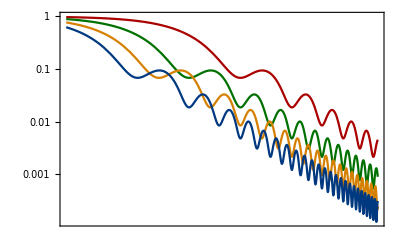

```mathematica
(* Pretty Plots *)
ws = Range[1,4];
cols = {RGBColor[Rational[2, 3], 0, 0],RGBColor[0, Rational[4, 9], 0],RGBColor[Rational[5, 6], Rational[1, 2], 0],RGBColor[0, Rational[2, 9], Rational[1, 2]]};
leg = LineLegend[ cols, ws , LegendLabel->MaTeX["w", Magnification->1.4] ];
frameticksString = { "\\pi/8", "\\pi/4", "\\pi/2", "\\pi", "2\\pi", "4\\pi"};
xaxisexponents = Range[-3,2];
xframeticks = Table[  {2^xaxisexponents[[j]] *  Pi, MaTeX[teststring[[j]], Magnification->1.3] }, {j,1,Length@xaxisexponents}];

EtrVsW = LogLogPlot[ Evaluate@Table[1- FidTr/2,{w,ws} ],{T,.3,20}
, PlotLabel->MaTeX["\\text{Inner product error within different subspaces}", Magnification->1.3]
, PlotLegends -> leg  
,PlotStyle->cols
, FrameLabel->{MaTeX["J T", Magnification->1.4], MaTeX[" 1 - \\frac{\\mathcal{F}_w}{2} ", Magnification->1.6 ] }
, FrameTicks->{ {Automatic, Automatic}, {xframeticks, None}  }
]
```

```mathematica
ns = {1,3,5, 8, 16, 128};
Ts = Range[.1, 20., .01];
traceerrorsvsN= Table[{T, traceError[n, T]}, {n,ns}, {T,Ts}];
```

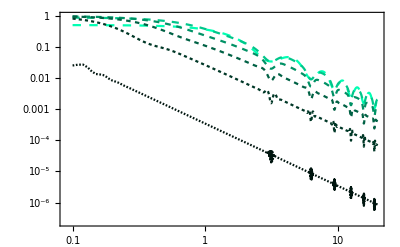

```mathematica
cols = Reverse@Table[ Hue[.45,  1, N@(j/Length@ns)^(1.4)   ], {j, 1, Length@ns} ];
dashes = Reverse@Table[  Dashing[.003 * j^.9] , {j,Length[ns]} ];
pltstyle= Table[ Directive[ cols[[j]], dashes[[j]] ], {j,1,Length[ns]}];
leg = LineLegend[ pltstyle, ns , LegendLabel->MaTeX["n", Magnification->1.4] ];

EtrVsTandN = ListLogLogPlot[ traceerrorsvsN
, PlotLabel->MaTeX["\\text{Inner product error decreases with } T \\text{ and } n", Magnification->1.3]
, PlotLegends -> leg  
,PlotStyle->pltstyle
, FrameLabel->{MaTeX["JT", Magnification->1.4], MaTeX[" \\mathcal{E}_\\text{tr} ", Magnification->2 ] }
, PlotMarkers->None
(* , GridLines->{Table[ j  Pi, {j,1,4}], {} } *)
, FrameTicks->{ {Automatic, Automatic}, {Table[ 2^j  Pi, {j,-4,4}], None}  }
(* (* Enable this to se the resolution *) , GridLines->{Select[Ts, .95 Pi<# < 1.05 Pi &], {}} , PlotRange->{ {.9 Pi, 1.1Pi} , Automatic } *)
]
```

```mathematica
Export[ "EtrVsW.pdf", EtrVsW ]
Export[ "EtrVsTandN.pdf", EtrVsTandN]
```

EtrVsW.pdf

EtrVsTandN.pdf

#### Sanity check: full matrix calculations, for Operator Norm errors.

```mathematica
Clear[n, T, A, w]
n= 5;
repl = A -> Pi/ 2 / T;

(* Analytical derivation *)
ham = w Z + A X;
Uw = FullSimplify @ MatrixExp[-I ham T /. repl] 
Urot = MatrixExp[ - I w Z T ] ;
```

{{Cos[1/2 √(π^2+4 T^2 w^2)]-(2 ⅈ T w Sin[1/2 √(π^2+4 T^2 w^2)])/(√(π^2+4 T^2 w^2)),-(ⅈ π Sin[1/2 √(π^2+4 T^2 w^2)])/(√(π^2+4 T^2 w^2))},{-(ⅈ π Sin[1/2 √(π^2+4 T^2 w^2)])/(√(π^2+4 T^2 w^2)),Cos[1/2 √(π^2+4 T^2 w^2)]+(2 ⅈ T w Sin[1/2 √(π^2+4 T^2 w^2)])/(√(π^2+4 T^2 w^2))}}

```mathematica
pauliExpansion[ mat_ ]:= Table[ Tr[ mat . sigma ], {sigma, {Id2, X, Y, Z} } ]/ 2;
pauliToNormal[ vec_ ]:= vec.{Id2,X,Y,Z};
```

```mathematica
diff = pauliExpansion[ Uw ] - pauliExpansion[ Urot ]
```

{1/2 (-ⅇ^(-ⅈ T w)-ⅇ^(ⅈ T w))+Cos[1/2 √(π^2+4 T^2 w^2)],-(ⅈ π Sin[1/2 √(π^2+4 T^2 w^2)])/(√(π^2+4 T^2 w^2)),0,1/2 (-ⅇ^(-ⅈ T w)+ⅇ^(ⅈ T w))-(2 ⅈ T w Sin[1/2 √(π^2+4 T^2 w^2)])/(√(π^2+4 T^2 w^2))}

```mathematica
evals = Norm[diff];
```

```mathematica
settings = {w -> 1, T-> 10};
evals /.settings //N
```

0.153249

```mathematica
Abs@Eigenvalues[ (Uw - Urot) /. settings ] // N
```

{0.153249,0.153249}

How do the operator norms behave, is the w=1 sector always the worst?

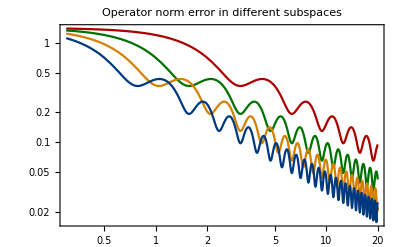

```mathematica
ws = Range[1,4];
cols =  ColorData[97, "ColorList"];
cols = {RGBColor[0.03529411764705882, 0.4392156862745098, 0.32941176470588235],RGBColor[0.396078431372549, 0.6, 1.],RGBColor[1., 0.8705882352941177, 0.],RGBColor[1., 0.6, 0.]};
cols = {RGBColor[0.028, 0.5376, 0.5936],Hue[0.07, 1, 0.75],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]};
cols = {RGBColor[Rational[2, 3], 0, 0],RGBColor[0, Rational[4, 9], 0],RGBColor[Rational[5, 6], Rational[1, 2], 0],RGBColor[0, Rational[2, 9], Rational[1, 2]]};

leg = LineLegend[ cols, ws , LegendLabel->MaTeX["w", Magnification->1.4] ];
EnormVsW = LogLogPlot[Evaluate@
Table[ Simplify[ evals ],{w,ws}]
,{T,.3,20}
, PlotLabel->"Operator norm error in different subspaces"
, PlotLegends -> leg  
,PlotStyle->cols
, FrameLabel->{MaTeX["J T", Magnification->1.4], MaTeX[" \\mathcal{E}_\\text{norm} ", Magnification->2 ] }
, FrameTicks->{ {Automatic, Automatic}, {Table[ 2^j  Pi, {j,-4,4}], None}  }

]
```

```mathematica
Export["EnormVsW.pdf", EnormVsW ]
```

EnormVsW.pdf

## v3.2. Derivation as in the paper (nov 2019):

Note, due to old conventions, q and w mean the same, namely the Hamming weigth of the controls. 

Note: If all control qubits have a coupling strength J to the target, then we have:

Ex = J (n-2q)/2
Δx = J(n -2q )
Δ0 = J(n - 2q0 )
d = (Δx - Δ0)/2 = -J (q-q0)
Choosing the Toffoli settings, i.e. q0 = n, we find Δ0 = -Jn, thus
d = (Δx - Δ0)/2  = - J (q-n)

(* Contrary to before, we now replace T by an expression for Omega *)

## The rotating frame

```mathematica
Clear[a,b,J,d, n, w, Om, T, phi ,om0,  Dx, D0 ];
simpl = Element[ {t,d,fi, n, J, w , w0, om0, Dx, D0}, Reals];

setOm = {T -> Pi / 2 / Om};
Htls = (Dx - om0 ) Z /2 + a X + b Y; MatrixForm[Htls]
HtlsTwoQuad = Htls /. {a -> Om Cos[ (D0 - om0) t + fi ], b -> Om Sin[ (D0 - om0) t + fi ] };
Uint = MatrixExp[ I  t  (D0-om0)  Z/2 ];
```

((Dx-om0)/2 | a-ⅈ b
a+ⅈ b | 1/2 (-Dx+om0))

```mathematica
FullSimplify[ I D[Uint, t] .  Uint†, simpl ] // MatrixForm
FullSimplify[ Uint.HtlsTwoQuad.Uint† ,  simpl ] // MatrixForm
```

(1/2 (-D0+om0) | 0
0 | (D0-om0)/2)

((Dx-om0)/2 | ⅇ^(-ⅈ fi) Om
ⅇ^(ⅈ fi) Om | 1/2 (-Dx+om0))

```mathematica
Hint= FullSimplify[  I D[Uint, t] . Uint† + Uint . HtlsTwoQuad . Uint†, simpl ] ;
Hint // MatrixForm
setD0 = D0 -> Dx - 2 d;
MatrixForm[ Hintd = Simplify[ Hint /. setD0 ]  ]
```

(1/2 (-D0+Dx) | ⅇ^(-ⅈ fi) Om
ⅇ^(ⅈ fi) Om | (D0-Dx)/2)

(d | ⅇ^(-ⅈ fi) Om
ⅇ^(ⅈ fi) Om | -d)

```mathematica
Uoffres = FullSimplify@ MatrixExp[ -I Hintd T  /.  setOm ]
```

{{Cos[(√(d^2+Om^2) π)/(2 Om)]-(ⅈ d Sin[(√(d^2+Om^2) π)/(2 Om)])/(√(d^2+Om^2)),(Om (-ⅈ Cos[fi]-Sin[fi]) Sin[(√(d^2+Om^2) π)/(2 Om)])/(√(d^2+Om^2))},{(Om (-ⅈ Cos[fi]+Sin[fi]) Sin[(√(d^2+Om^2) π)/(2 Om)])/(√(d^2+Om^2)),Cos[(√(d^2+Om^2) π)/(2 Om)]+(ⅈ d Sin[(√(d^2+Om^2) π)/(2 Om)])/(√(d^2+Om^2))}}

Above, we reproduced Eq. 8. and 9.

## The errors

Now, we assume permutation symmetry among all qubits, and that the subspace w0 = n is resonant. Thus:
d = - J (w-n).

```mathematica
setd = d -> -J (w-n);
Htilde = Simplify[ Hint /. setD0 /. setd ];
Htilde // MatrixForm

Uoffres = FullSimplify[ MatrixExp[ -I Htilde t /. setd ] ,  simpl ];
(* Uoffres // MatrixForm *)
UoffresGoal = Simplify[ Uoffres /. Om -> 0, simpl ];
UoffresGoal // MatrixForm
UoffresGoalconj = MatrixExp[ +I Htilde t /. setd /. Om -> 0 ]; (* Note the +I rotation direction, for conjugate *)
```

(J (n-w) | ⅇ^(-ⅈ fi) Om
ⅇ^(ⅈ fi) Om | J (-n+w))

(Cos[J t (n-w)]-ⅈ Sin[J t (n-w)] | 0
0 | Cos[J t (n-w)]+ⅈ Sin[J t (n-w)])

### Trace errors (iToffoli)

#### Derivation

```mathematica
tracePerw =FullSimplify[ ExpToTrig[ (1/2)  Tr[ Uoffres . UoffresGoalconj ] ], simpl ]
```

Cos[t √(Om^2+J^2 (n-w)^2)] Cos[J t (n-w)]+(J (n-w) Sin[t √(Om^2+J^2 (n-w)^2)] Sin[J t (n-w)])/(√(Om^2+J^2 (n-w)^2))

Expressing in terms of J/Om:

```mathematica
setNu = { √(Om^2+J^2 (n-w)^2) -> Om √(1 + (n-w)^2 J^2 / Om^2)};
Fidw = tracePerw /.t-> T  /. setOm /. setNu
```

Cos[1/2 π √(1+(J^2 (n-w)^2)/Om^2)] Cos[(J π (n-w))/(2 Om)]+(J (n-w) Sin[1/2 π √(1+(J^2 (n-w)^2)/Om^2)] Sin[(J π (n-w))/(2 Om)])/(√(Om^2+J^2 (n-w)^2))

```mathematica
(* Let's make a function out of this! *)
FidwPerN[ n_] := 2 Cos[1/2 π √(1+(J^2 (n-w)^2)/Om^2)] Cos[(J π (n-w))/(2 Om)]+(2 J (n-w) Sin[1/2 π √(1+(J^2 (n-w)^2)/Om^2)] Sin[(J π (n-w))/(2 Om)])/(√(Om^2+J^2 (n-w)^2)) /. Om -> 1 ;
```

```mathematica
(* Pretty notation in paper *)
```

```mathematica
setGamma = (J  (n-w))/Om -> γ;
setGamma2 = J -> γ Om / (n-w) ;
 Fidw /. setGamma2
```

Cos[(π γ)/2] Cos[1/2 π √(1+γ^2)]+(Om γ Sin[(π γ)/2] Sin[1/2 π √(1+γ^2)])/(√(Om^2+Om^2 γ^2))

#### Plotting trace errors:

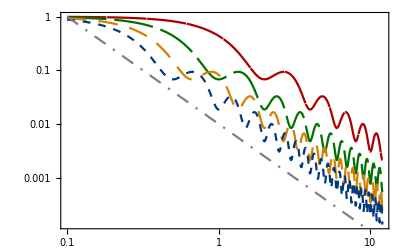

```mathematica
(* Plotting Fidw for Trace Error per subspace: *)
ws = Range[1,4];
cols = {RGBColor[Rational[2, 3], 0, 0],RGBColor[0, Rational[4, 9], 0],RGBColor[Rational[5, 6], Rational[1, 2], 0],RGBColor[0, Rational[2, 9], Rational[1, 2]]};
dashes = .07 { {1,0}, {1,.2}, {.5,.3}, {.2,.2} };
pltstyle = Table[ Directive[ cols[[j]], Dashing[ dashes[[j]] ] ], {j,1,4} ];
leg = LineLegend[ 
pltstyle
, Table[ MaTeX[ "n-"<> ToString[ w ], Magnification->1.4 ], {w,ws} ] 
, LegendLabel->MaTeX["\\text{Weight } q", Magnification->1.4] 
];

EtrVsHighestWbare = LogLogPlot[ Evaluate@Table[1- Fidw /. {Om-> 1, (n-w) -> deltaW},{deltaW,ws} ],{J,.1,12}
(* , PlotLabel->MaTeX["\\text{Inner product error within different subspaces}", Magnification->1.3] *)
, PlotLegends -> leg
,PlotStyle->pltstyle
, FrameLabel->{MaTeX["J/\\Omega", Magnification->1.5], MaTeX[" 1 - \\mathcal{F}_q ", Magnification->1.6 ] }
(* , FrameTicks->{ {Automatic, Automatic}, {xframeticks, None}  } *)
, ImageSize->405
];

(* Show the plot together with the line T^-2 *)
PolyDecayPlot = LogLogPlot[ { .01 x^-2 }, {x,.1,12} , PlotStyle-> { Dashing[ .04 {.6,.4,.1,.4}], Gray}  , PlotLegends-> {MaTeX[ "( J / \\Omega)^{-2} " , Magnification-> 1.4]  } ];

EtrVsHighestW = Show[ { EtrVsHighestWbare, PolyDecayPlot } ]
```

```mathematica
Export[ "EtrVsHighestW.pdf", EtrVsHighestW ]
```

EtrVsHighestW.pdf

#### Plotting the Process Fidelity:

```mathematica
(* Plotting the cummulative trace error. It's always perfect when w=n, while we require Fidw for w={0...n-1}  *)
Etr[n_]:= 1 - (1/2^(n+1)) * ( 2 + Simplify@Sum[ N[ FidwPerN[n] /. {Om -> 1} ] *   Binomial[n,w]  , {w,0,n-1}] ) ;

(* Converting to Process Fidelity.  d is the dimensionality of Hilbert space. Result below follows from Nielsen / Horodecki  *)
ProcessFidFromTraceFid[ traceFid_, d_  ]:= (d  Abs[traceFid]^2 + 1 ) / (d+1)
ProcFidPerN[ n_ ]:= ProcessFidFromTraceFid[ 1 - Etr[ n ], 2^(n+1) ];

(* Sanity check: *)
N[ ProcFidPerN[ 2 ] /. J -> 1 ] 
N[ ProcFidPerN[ 2 ] /. J -> 5 ]
```

0.630398

0.971092

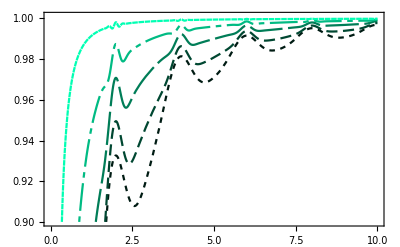

```mathematica
ns = {2,4,6,9,20};
cols = Table[ Hue[.45,  1, N@(j/Length@ns)^(1.4)   ], {j, 1, Length@ns} ];
dashes = Dashing /@ ( .01 {   {1,1}, {2,1}, {6,1} , {1,1,5,1}, {1,0} } );
pltstyle= Table[ Directive[ cols[[j]], dashes[[j]] ], {j,1,Length[ns]}];
leg = LineLegend[ pltstyle, ns , LegendLabel->MaTeX["n", Magnification->1.4] ];


ProcFidvsTandN = Plot[ Evaluate@Table[ ProcFidPerN[n], {n,ns}], {J,.1, 10 }
(* , PlotLabel->MaTeX["\\text{Process fidelity increases with } n", Magnification->1.3] *)
, PlotLegends -> leg  
,PlotStyle->pltstyle
, FrameLabel->{MaTeX["J/\\Omega", Magnification->1.5], MaTeX[" \\bar{F} ", Magnification->2 ] }
(* , GridLines->{Table[ j  Pi, {j,1,4}], {} } *)
(* , FrameTicks->{ {Automatic, Automatic}, {xframeticks, None}  } *)
, ImageSize->400
(* , MaxRecursion->9 (* Needed to get all features in the plot for high n *) *)
(* , PlotPoints->50 *)
, PlotRange->{0.9,1.001}
]
```

```mathematica
Export[ "FidProcvsTandN.pdf", ProcFidvsTandN ]
```

FidProcvsTandN.pdf

### Norm error

#### Derivation

```mathematica
Udifference = Uoffres - UoffresGoal /. t-> T /. setOm /. setNu
```

{{-ⅇ^(-(ⅈ J π (n-w))/(2 Om))+Cos[1/2 π √(1+(J^2 (n-w)^2)/Om^2)]-(ⅈ J (n-w) Sin[1/2 π √(1+(J^2 (n-w)^2)/Om^2)])/(√(Om^2+J^2 (n-w)^2)),(Om (-ⅈ Cos[fi]-Sin[fi]) Sin[1/2 π √(1+(J^2 (n-w)^2)/Om^2)])/(√(Om^2+J^2 (n-w)^2))},{(Om (-ⅈ Cos[fi]+Sin[fi]) Sin[1/2 π √(1+(J^2 (n-w)^2)/Om^2)])/(√(Om^2+J^2 (n-w)^2)),-ⅇ^((ⅈ J π (n-w))/(2 Om))+Cos[1/2 π √(1+(J^2 (n-w)^2)/Om^2)]+(ⅈ J (n-w) Sin[1/2 π √(1+(J^2 (n-w)^2)/Om^2)])/(√(Om^2+J^2 (n-w)^2))}}

```mathematica
(* Express in terms of γ, and per operator:  *)
setGamma = (J  (n-w))/Om -> γ;
setGamma2 = J -> γ Om / (n-w) ;

parId = FullSimplify@ ExpToTrig[ Tr[Udifference]/2 /. setGamma2  ] 
parZ = FullSimplify@ExpToTrig[ Tr[Udifference.Z  ]/2 /. setGamma2]
parX = FullSimplify@ExpToTrig@Tr[Udifference.(Cos[fi] X + Sin[fi] Y) /. setGamma2 ] / 2
parOrthogonal = FullSimplify@ExpToTrig@Tr[Udifference.(Sin[fi] X - Cos[fi] Y)] / 2
```

-Cos[(π γ)/2]+Cos[1/2 π √(1+γ^2)]

ⅈ (Sin[(π γ)/2]-(Om γ Sin[1/2 π √(1+γ^2)])/(√(Om^2 (1+γ^2))))

-(ⅈ Om Sin[1/2 π √(1+γ^2)])/(√(Om^2 (1+γ^2)))

0

```mathematica
UdiffShort = Simplify@ExpToTrig@FullSimplify[ Udifference /. Om-> 1 /. fi -> 0 /. n ->  deltaW+w  ]
```

{{-Cos[(deltaW J π)/2]+Cos[1/2 √(1+deltaW^2 J^2) π]+ⅈ (Sin[(deltaW J π)/2]-(deltaW J Sin[1/2 √(1+deltaW^2 J^2) π])/(√(1+deltaW^2 J^2))),-(ⅈ Sin[1/2 √(1+deltaW^2 J^2) π])/(√(1+deltaW^2 J^2))},{-(ⅈ Sin[1/2 √(1+deltaW^2 J^2) π])/(√(1+deltaW^2 J^2)),-Cos[(deltaW J π)/2]+Cos[1/2 √(1+deltaW^2 J^2) π]-ⅈ (Sin[(deltaW J π)/2]-(deltaW J Sin[1/2 √(1+deltaW^2 J^2) π])/(√(1+deltaW^2 J^2)))}}

This one takes a long time to evaluate... but after a while, it returns a single line solution! Note that all J’s should be read as J/Omega.

```mathematica
UdiffNorm = Simplify[ Norm[ UdiffShort  ], { Element[ J, Reals] , Element[ deltaW, Integers] }]
```

√(2-2 Cos[(deltaW J π)/2] Cos[1/2 √(1+deltaW^2 J^2) π]-(2 deltaW J Sin[(deltaW J π)/2] Sin[1/2 √(1+deltaW^2 J^2) π])/(√(1+deltaW^2 J^2)))

The norm error over ALL subspaces together is the worst case scenario:

```mathematica
Simplify[ UdiffNorm /. deltaW -> 1 ]
```

√(2-2 Cos[(J π)/2] Cos[1/2 √(1+J^2) π]-(2 J Sin[(J π)/2] Sin[1/2 √(1+J^2) π])/(√(1+J^2)))

#### The norm error

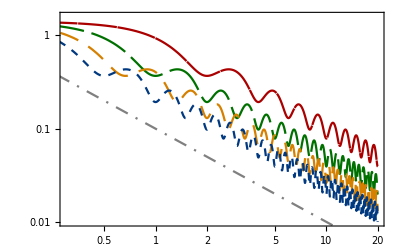

```mathematica
deltaWs = Range[1,4];
cols = {RGBColor[Rational[2, 3], 0, 0],RGBColor[0, Rational[4, 9], 0],RGBColor[Rational[5, 6], Rational[1, 2], 0],RGBColor[0, Rational[2, 9], Rational[1, 2]]};
dashes = .07 { {1,0}, {1,.2}, {.5,.3}, {.2,.2} };
pltstyle = Table[ Directive[ cols[[j]], Dashing[ dashes[[j]] ] ], {j,1,4} ];
leg = LineLegend[ 
pltstyle
, Table[ MaTeX[ "n-"<> ToString[ w ], Magnification->1.4 ], {w,ws} ] 
, LegendLabel->MaTeX["\\text{Weight } q", Magnification->1.4] 
];

EnormVsHighestWbare = Legended[ 
Show[Table[
LogLogPlot[ UdiffNorm /. deltaW -> deltaWs[[wIdx]], {J,.1,20} 
(* , PlotLabel->MaTeX["\\text{Operator norm error in different subspaces}", Magnification->1.3 ] *)
, PlotStyle->pltstyle[[wIdx]]
, FrameLabel->{MaTeX["J/\\Omega", Magnification->1.5], MaTeX[" \\mathcal{E}_{ \\text{norm}, q} ", Magnification->2 ] }
, ImageSize->400
, PlotRange->{{.3,20}, {10^-2, 1.6} }

]
,{wIdx, 1, Length@deltaWs }  ] ]
, leg ] ;

(* Show the plot together with the line T^-2 *)
LinDecayPlot = LogLogPlot[ { .1  x^-1 }, {x,.1,12} , PlotStyle-> { Dashing[ .04 {.6,.4,.1,.4}], Gray}  , PlotLegends-> {MaTeX[ "( J / \\Omega)^{-1} " , Magnification-> 1.4]  } ];

EnormVsHighestW = Show[ { EnormVsHighestWbare, LinDecayPlot } ]
```

```mathematica
Export[ "EnormVsHighestW.pdf", EnormVsHighestW ]
```

EnormVsHighestW.pdf

## Another case: The 2T operation, required for the Toffoli gate

```mathematica
(* For the Toffoli, we do the same derivation, but with double-time T. *)
setOmToffoli = T-> Pi/Om;
UoffresToff = FullSimplify@MatrixExp[ -I Hintd T /. setOmToffoli ]
```

{{Cos[(√(d^2+Om^2) π)/Om]-(ⅈ d Sin[(√(d^2+Om^2) π)/Om])/(√(d^2+Om^2)),(Om (-ⅈ Cos[fi]-Sin[fi]) Sin[(√(d^2+Om^2) π)/Om])/(√(d^2+Om^2))},{(Om (-ⅈ Cos[fi]+Sin[fi]) Sin[(√(d^2+Om^2) π)/Om])/(√(d^2+Om^2)),Cos[(√(d^2+Om^2) π)/Om]+(ⅈ d Sin[(√(d^2+Om^2) π)/Om])/(√(d^2+Om^2))}}

```mathematica
setd = d -> -J (w-n);
setGamma2 = J -> γ Om / (n-w) ;
Ugate = UoffresToff /. setd /. fi -> 0 ;

(* Make Ugoal *)
Htilde = Simplify[ Hint /. setD0 /. setd ];
UgoalConj = MatrixExp[ +I Htilde T /. setd /. Om -> 0 /. setOmToffoli ];

(* Calc fidelity and compare with previous result: *)
tracePerWToff = FullSimplify[ 1/2 *  ExpToTrig@ Tr[ UgoalConj . Ugate ]  /. setGamma2  ]
tracePerWiToff = Fidw /. setGamma2 /. Om -> 1
```

Cos[π γ] Cos[π √(1+γ^2)]+(γ Sin[π γ] Sin[π √(1+γ^2)])/(√(1+γ^2))

Cos[(π γ)/2] Cos[1/2 π √(1+γ^2)]+(γ Sin[(π γ)/2] Sin[1/2 π √(1+γ^2)])/(√(1+γ^2))

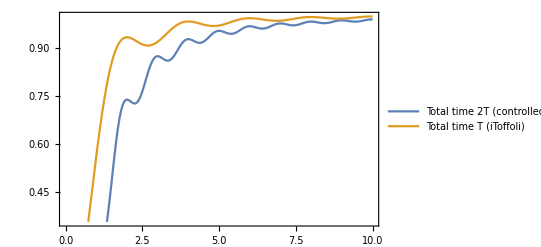

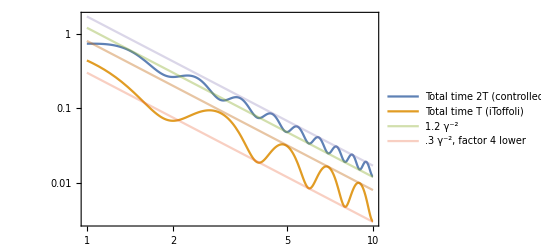

```mathematica
(* Fidelity as function of γ. Compare with 'normal T' result: *)
Plot[ {tracePerWToff, tracePerWiToff}, {γ, 0,10}, PlotLegends->{"Total time 2T (controlled-Z)", "Total time T (iToffoli)"} ]

LogLogPlot[ {1-tracePerWToff, 1-tracePerWiToff, 1.2 γ^-2, .3 γ^-2,1.7 γ^-2, .8 γ^-2 }, {γ, 1,10}
, PlotStyle-> {Automatic, Automatic, Opacity[.4], Opacity[.3], Opacity[.3], Opacity[.4]}
 ,PlotLegends->{"Total time 2T (controlled-Z)", "Total time T (iToffoli)", "1.2 γ^-2", ".3 γ^-2, factor 4 lower" } ]
```

## v3: [OLD] The neat stuff: Paper equation check, and plots

#### Rotating frame

```mathematica
Clear[a,b,J,d, n, w, Om, T, phi];
simpl = Element[ {t,d,fi}, Reals];
setOm = {Om -> Pi / 2 / T };
Htls = J(n/2 - w) Z + a X + b Y; MatrixForm[Htls]
HtlsTwoQuad = ({{J (n/2-w), Om Exp[ -I d t - I fi]}, {Om Exp[+I d t+I fi], -J (n/2-w)}});
Uint = MatrixExp[ I d t Z/2 ];
```

(J (n/2-w) | a-ⅈ b
a+ⅈ b | -J (n/2-w))

```mathematica
FullSimplify[ I D[Uint, t] .  Uint†, simpl ] // MatrixForm
FullSimplify[ Uint.HtlsTwoQuad.Uint† ,  simpl ] // MatrixForm
```

(-d/2 | 0
0 | d/2)

(1/2 J (n-2 w) | ⅇ^(-ⅈ fi) Om
ⅇ^(ⅈ fi) Om | J (-n/2+w))

```mathematica
Htilde= FullSimplify[  I D[Uint, t] . Uint† + Uint . HtlsTwoQuad . Uint†, simpl ] ;
Htilde // MatrixForm
```

(1/2 (-d+J (n-2 w)) | ⅇ^(-ⅈ fi) Om
ⅇ^(ⅈ fi) Om | 1/2 (d-J n+2 J w))

```mathematica
Uoffres = FullSimplify@ MatrixExp[ -I Htilde T /. setOm ]
```

{{Cos[1/2 √(π^2+T^2 (d-J n+2 J w)^2)]+(ⅈ T (d-J n+2 J w) Sin[1/2 √(π^2+T^2 (d-J n+2 J w)^2)])/(√(π^2+T^2 (d-J n+2 J w)^2)),(π (-ⅈ Cos[fi]-Sin[fi]) Sin[1/2 √(π^2+T^2 (d-J n+2 J w)^2)])/(√(π^2+T^2 (d-J n+2 J w)^2))},{(π (-ⅈ Cos[fi]+Sin[fi]) Sin[1/2 √(π^2+T^2 (d-J n+2 J w)^2)])/(√(π^2+T^2 (d-J n+2 J w)^2)),Cos[1/2 √(π^2+T^2 (d-J n+2 J w)^2)]-(ⅈ T (d-J n+2 J w) Sin[1/2 √(π^2+T^2 (d-J n+2 J w)^2)])/(√(π^2+T^2 (d-J n+2 J w)^2))}}

#### The trace error

Now specializing to w0 = 0, we find the trace error (within the subspace with fixed w):

```mathematica
setd = {d -> J n};
Htilde /. setd // Simplify // MatrixForm
```

(-J w | ⅇ^(-ⅈ fi) Om
ⅇ^(ⅈ fi) Om | J w)

```mathematica
Uoffres = FullSimplify[ MatrixExp[ -I Htilde t /. setd ] ,  simpl ];
Uoffres // MatrixForm
UoffresGoalconj = MatrixExp[ +I Htilde t /. setd /. Om -> 0 ]; (* Note the +I rotation direction, for conjugate *)
tracePerw =FullSimplify [ Tr[ Uoffres . UoffresGoalconj ], simpl ]
```

(Cos[t √(Om^2+J^2 w^2)]+(ⅈ J w Sin[t √(Om^2+J^2 w^2)])/(√(Om^2+J^2 w^2)) | (Om (-ⅈ Cos[fi]-Sin[fi]) Sin[t √(Om^2+J^2 w^2)])/(√(Om^2+J^2 w^2))
(Om (-ⅈ Cos[fi]+Sin[fi]) Sin[t √(Om^2+J^2 w^2)])/(√(Om^2+J^2 w^2)) | Cos[t √(Om^2+J^2 w^2)]-(ⅈ J w Sin[t √(Om^2+J^2 w^2)])/(√(Om^2+J^2 w^2)))

2 Cos[J t w] Cos[t √(Om^2+J^2 w^2)]+(2 J w Sin[J t w] Sin[t √(Om^2+J^2 w^2)])/(√(Om^2+J^2 w^2))

Expressing in terms of JT:

```mathematica
setNu = { √(Om^2+J^2 w^2) -> J √(Om^2/ J^2+w^2)};
Fidw = tracePerw /.t-> T /.  setNu /. setOm
```

2 Cos[J T w] Cos[J T √(π^2/(4 J^2 T^2)+w^2)]+(2 J w Sin[J T w] Sin[J T √(π^2/(4 J^2 T^2)+w^2)])/(√(π^2/(4 T^2)+J^2 w^2))

```mathematica
Tr[ Uoffres ]
```

2 Cos[t √(Om^2+J^2 w^2)]

#### Plotting trace errors:

```mathematica
(* Setting up pretty frameticks *)
frameticksString = { "\\pi/8", "\\pi/4", "\\pi/2", "\\pi", "2\\pi", "4\\pi"};
xaxisexponents = Range[-3,2];
xframeticks = Table[  {2^xaxisexponents[[j]] *  Pi, MaTeX[frameticksString[[j]], Magnification->1.3] }, {j,1,Length@xaxisexponents}];
```

```mathematica
(* Plotting Fidw for Trace Error per subspace: *)
ws = Range[1,4];
cols = {RGBColor[Rational[2, 3], 0, 0],RGBColor[0, Rational[4, 9], 0],RGBColor[Rational[5, 6], Rational[1, 2], 0],RGBColor[0, Rational[2, 9], Rational[1, 2]]};
leg = LineLegend[ cols, ws , LegendLabel->MaTeX["q", Magnification->1.4] ];

EtrVsW = LogLogPlot[ Evaluate@Table[1- Fidw/2 /. J-> 1,{w,ws} ],{T,.3,20}
, PlotLabel->MaTeX["\\text{Inner product error within different subspaces}", Magnification->1.3]
, PlotLegends -> leg  
,PlotStyle->cols
, FrameLabel->{MaTeX["J T", Magnification->1.4], MaTeX[" 1 - \\frac{\\mathcal{F}_q}{2} ", Magnification->1.6 ] }
, FrameTicks->{ {Automatic, Automatic}, {xframeticks, None}  }
, ImageSize->400
]
```

-Graphics-

```mathematica
(* Plotting the cummulative trace error *)
Etr[n_]:= 1 - (1/2^(n+1)) * ( 2 + Sum[ Fidw *   Binomial[n,w], {w,1,n}] ) /. J -> 1;
```

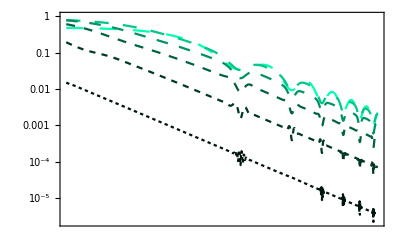

```mathematica
ns = {1,3,5, 8, 16,64};
cols = Reverse@Table[ Hue[.45,  1, N@(j/Length@ns)^(1.4)   ], {j, 1, Length@ns} ];
dashes = Reverse@Table[  Dashing[.006 * j^.9] , {j,Length[ns]} ];
pltstyle= Table[ Directive[ cols[[j]], dashes[[j]] ], {j,1,Length[ns]}];
leg = LineLegend[ pltstyle, ns , LegendLabel->MaTeX["n", Magnification->1.4] ];

EtrVsTandN = LogLogPlot[ Evaluate@Table[ Etr[n], {n,ns}], {T,.3, 20 }
, PlotLabel->MaTeX["\\text{Inner product error decreases with } T \\text{ and } n", Magnification->1.3]
, PlotLegends -> leg  
,PlotStyle->pltstyle
, FrameLabel->{MaTeX["JT", Magnification->1.4], MaTeX[" \\mathcal{E}_\\text{tr} ", Magnification->2 ] }
(* , GridLines->{Table[ j  Pi, {j,1,4}], {} } *)
, FrameTicks->{ {Automatic, Automatic}, {xframeticks, None}  }
, ImageSize->400
(* , MaxRecursion->9 (* Needed to get all features in the plot for high n *) *)
, PlotPoints->20
]
```

```mathematica
Export[ "EtrVsW.pdf", EtrVsW ]
Export[ "EtrVsTandN.pdf", EtrVsTandN]
```

EtrVsW.pdf

EtrVsTandN.pdf

```mathematica
dashes
```

{Dashing[0.0300945],Dashing[0.0255402],Dashing[0.0208932],Dashing[0.0161273],Dashing[0.0111964],Dashing[0.006]}

```mathematica
dashes = Reverse@Table[  Dashing[.006 * j^.9] , {j,Length[ns]} ]
```

{Dashing[0.0300945],Dashing[0.0255402],Dashing[0.0208932],Dashing[0.0161273],Dashing[0.0111964],Dashing[0.006]}

#### Relating the “Process Fidelity” to our Trace Norm (BUT see a better derivation in part 3.1!)

```mathematica
(* d is the dimensionality of Hilbert space. Result below follows from Nielsen  *)
ProcessFidFromTraceFid[ traceFid_, d_  ]:= (d  Abs[traceFid]^2 + 1 ) / (d+1)
ProcFidPerN[ n_ ]:= ProcessFidFromTraceFid[ 1 - Etr[ n ], 2^(n+1) ];

N[ ProcFidPerN[3] /. T-> 1 ]
```

0.426963

{Dashing[0.],Dashing[0.01],Dashing[0.03]}

{{6.28319,4},{9.42478,6},{12.5664,8},{15.708,10},{18.8496,12},{21.9911,14},{25.1327,16},{28.2743,18},{31.4159,20}}

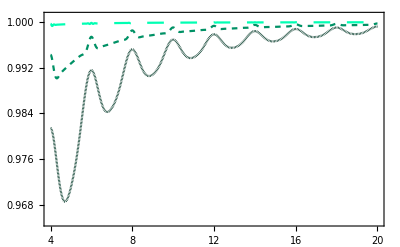

```mathematica
ns = {2,7,25};

cols = Table[ Hue[.45,  1, N@(j/Length@ns)^(1.4)   ], {j, 1, Length@ns} ];
dashes = Dashing /@ ( .01 {   0, 1, 3 } )
pltstyle= Table[ Directive[ cols[[j]], dashes[[j]] ], {j,1,Length[ns]}];
leg = LineLegend[ pltstyle, ns , LegendLabel->MaTeX["n", Magnification->1.4] ];


(* Note that that scale J/Ω differs from JT by a factor of Pi/2! *)
xframeticks = Table[ { N[ Pi / 2 * j] , j   }, {j,4,20,2}]


ProcFidvsTandN = Plot[ Evaluate@Table[ ProcFidPerN[n], {n,ns}], {T,4*Pi/2, 20*Pi/2 }
, PlotLabel->MaTeX["\\text{Process fidelity increases with } n", Magnification->1.3]
, PlotLegends -> leg  
,PlotStyle->pltstyle
, FrameLabel->{MaTeX["J/\\Omega", Magnification->1.4], MaTeX[" \\bar{F} ", Magnification->2 ] }
(* , GridLines->{Table[ j  Pi, {j,1,4}], {} } *)
, FrameTicks->{ {Automatic, Automatic}, {xframeticks, None}  }
, ImageSize->400
(* , MaxRecursion->9 (* Needed to get all features in the plot for high n *) *)
, PlotPoints->30
, PlotRange->{0.965,1.001}
]
```

#### Plotting Norm error, a variation where q_0=n is resonant!

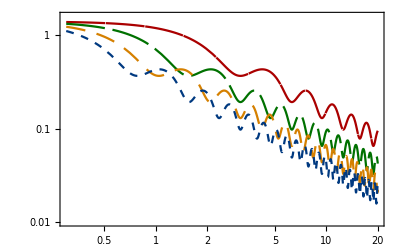

```mathematica
(* Plotting Fidw for Norm Error per subspace: *)
ws = Range[1,4];
cols = {RGBColor[Rational[2, 3], 0, 0],RGBColor[0, Rational[4, 9], 0],RGBColor[Rational[5, 6], Rational[1, 2], 0],RGBColor[0, Rational[2, 9], Rational[1, 2]]};
dashes = .07 { {1,0}, {1,.2}, {.5,.3}, {.2,.2} };
pltstyle = Table[ Directive[ cols[[j]], Dashing[ dashes[[j]] ] ], {j,1,4} ];
leg = LineLegend[ pltstyle, ws , LegendLabel->MaTeX["n-q", Magnification->1.4] ];

EnormVsHighestW = Legended[ 
Show[Table[
LogLogPlot[ Norm[ UdiffPlotable  ], {T,.3, 20} 
, PlotLabel->MaTeX["\\text{Operator norm error in different subspaces}", Magnification->1.3 ]
, PlotStyle->pltstyle[[w]]
, FrameLabel->{MaTeX["J T", Magnification->1.4], MaTeX[" \\mathcal{E}_{ \\text{norm}, q} ", Magnification->2 ] }
, FrameTicks->{ {Automatic, Automatic}, {xframeticks, None}  }
, ImageSize->400
, PlotRange->{{.3,20}, {10^-2, 1.6} }

]
,{w,1,4}  ] ]
, leg ]
```

```mathematica
Export[ "EnormVsHighestW.pdf", EnormVsHighestW ]
```

EnormVsHighestW.pdf

#### Plotting Norm error (old version)

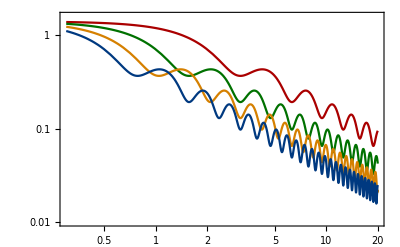

```mathematica
(* Plotting Fidw for Norm Error per subspace: *)
ws = Range[1,4];
cols = {RGBColor[Rational[2, 3], 0, 0],RGBColor[0, Rational[4, 9], 0],RGBColor[Rational[5, 6], Rational[1, 2], 0],RGBColor[0, Rational[2, 9], Rational[1, 2]]};
leg = LineLegend[ cols, ws , LegendLabel->MaTeX["q", Magnification->1.4] ];

EnormVsW = Legended[ 
Show[Table[
LogLogPlot[ Norm[ UdiffPlotable  ], {T,.3, 20} 
, PlotLabel->MaTeX["\\text{Operator norm error in different subspaces}", Magnification->1.3 ]
, PlotStyle->cols[[w]]
, FrameLabel->{MaTeX["J T", Magnification->1.4], MaTeX[" \\mathcal{E}_{ \\text{norm}, q} ", Magnification->2 ] }
, FrameTicks->{ {Automatic, Automatic}, {xframeticks, None}  }
, ImageSize->400
, PlotRange->{{.3,20}, {10^-2, 1.6} }

]
,{w,1,4}  ] ]
, leg ]
```

## v4: [OLD] Paper equation checks, but with non-star couplings.

#### Rotating frame

```mathematica
Clear[J, E0, n, w, dres, dx,Om, T, phi];
simpl = Element[ {t,dx,dres,fi, E0}, Reals];
setOm = {Om -> Pi / 2 / T };
Htls = d/2 Z + a X + b Y + E0 Id2; MatrixForm[Htls]
HtlsTwoQuad = ({{dx/2 + E0, Om Exp[ -I dres t - I fi]}, {Om Exp[+I dres t+I fi], -dx/2 + E0}}); HtlsTwoQuad // MatrixForm
Uint = MatrixExp[ I dres t Z/2  + I Id2 E0 t];
```

(d/2+E0 | a-ⅈ b
a+ⅈ b | -d/2+E0)

(dx/2+E0 | ⅇ^(-ⅈ fi-ⅈ dres t) Om
ⅇ^(ⅈ fi+ⅈ dres t) Om | -dx/2+E0)

```mathematica
FullSimplify[ I D[Uint, t] .  Uint†, simpl ] // MatrixForm
FullSimplify[ Uint.HtlsTwoQuad.Uint† ,  simpl ] // MatrixForm
```

(-dres/2-E0 | -E0
-E0 | 1/2 (dres-2 E0))

$Aborted

Calculate the rotating frame Hamiltonian:

```mathematica
term1 = FullSimplify[ I D[Uint, t] .  Uint†, simpl ] ; term1 // MatrixForm
term2 = FullSimplify[ Uint.HtlsTwoQuad.Uint† ,  simpl ]; term2 // MatrixForm (* We know E0 cancels here *)
Htilde = Simplify[ term1 + term2 ]; Htilde // MatrixForm
```

(-dres/2-E0 | 0
0 | 1/2 (dres-2 E0))

(dx/2+E0 | ⅇ^(-ⅈ fi) Om
ⅇ^(ⅈ fi) Om | -dx/2+E0)

(1/2 (-dres+dx) | ⅇ^(-ⅈ fi) Om
ⅇ^(ⅈ fi) Om | (dres-dx)/2)